# Weighted Rotation Averaging - 300 Random ---------------------------------------------------------------------------

## Rotation Averaging - Drill:

In this part we will display tutorial for rotation averaging based on the non-Abelian Kuramoto model. Three dimensional data is given as rotational SO(3) matrices. Weights are given as random numbers from 0 to 1.

Step 1) First we need to install Rotation package that is also given in this folder and is named as Rotation.m

Step 2) Include real dataset Drill

```mathematica
poc=Import["C:\\Users\\WWTDev - Zinaid\\Desktop\\ROTATION WOLFRAM PACKAGE\\Rotation Averaging\\Rotation Average Weighted - 300 Random\\300.csv"];
```

Step 3) Function for converting quaternion to matrix

```mathematica
toMatrix[kvat_]:={{1-2 kvat[[3]]^2-2 kvat[[4]]^2,2kvat[[2]]kvat[[3]]-2kvat[[4]]kvat[[1]],2kvat[[2]]kvat[[4]]+2kvat[[3]]kvat[[1]]},{2kvat[[2]]kvat[[3]]+2kvat[[4]]kvat[[1]],1-2 kvat[[2]]^2-2 kvat[[4]]^2,2kvat[[3]]kvat[[4]]-2kvat[[2]]kvat[[1]]},{2kvat[[2]]kvat[[4]]-2kvat[[3]]kvat[[1]],2kvat[[3]]kvat[[4]]+2kvat[[2]]kvat[[1]],1-2 kvat[[2]]^2-2 kvat[[3]]^2}};
```

Step 4) Include arithmetic and geometric average and weights

```mathematica
projmean=toMatrix[Flatten[Import["C:\\Users\\WWTDev - Zinaid\\Desktop\\ROTATION WOLFRAM PACKAGE\\Rotation Averaging\\Rotation Average Weighted - 300 Random\\300_proj_mean.csv"]]];
```

```mathematica
geommean=toMatrix[Flatten[Import["C:\\Users\\WWTDev - Zinaid\\Desktop\\ROTATION WOLFRAM PACKAGE\\Rotation Averaging\\Rotation Average Weighted - 300 Random\\300_geom_mean.csv"]]];
```

```mathematica
wam=Flatten[Import["C:\\Users\\WWTDev - Zinaid\\Desktop\\ROTATION WOLFRAM PACKAGE\\Rotation Averaging\\Rotation Average Weighted - 300 Random\\300_weights.csv"]];
```

Step 5) Define model

```mathematica
n=300;
K=30;
eqns=Table[{Subscript[x1,i]'[t]==-2Subscript[x1,i][t] Subscript[x2,i][t] (K/(2n)Sum[wam[[j]]Subscript[x2,j][t],{j,1,n}])-2Subscript[x1,i][t] Subscript[x3,i][t] (K/(2n)Sum[wam[[j]]Subscript[x3,j][t],{j,1,n}])-2Subscript[x1,i][t] Subscript[x4,i][t] (K/(2n)Sum[wam[[j]]Subscript[x4,j][t],{j,1,n}])+((Subscript[x1,i][t])^2-(Subscript[x2,i][t])^2-(Subscript[x3,i][t])^2-(Subscript[x4,i][t])^2-1)(-K/(2n)Sum[wam[[j]]Subscript[x1,j][t],{j,1,n}]),Subscript[x2,i]'[t]==2Subscript[x1,i][t] Subscript[x2,i][t] (-K/(2n)Sum[wam[[j]]Subscript[x1,j][t],{j,1,n}])-2Subscript[x2,i][t] Subscript[x3,i][t] (K/(2n)Sum[wam[[j]]Subscript[x3,j][t],{j,1,n}])-2Subscript[x2,i][t] Subscript[x4,i][t] (K/(2n)Sum[wam[[j]]Subscript[x4,j][t],{j,1,n}])+((Subscript[x1,i][t])^2-(Subscript[x2,i][t])^2+(Subscript[x3,i][t])^2+(Subscript[x4,i][t])^2+1)(K/(2n)Sum[wam[[j]]Subscript[x2,j][t],{j,1,n}]),
Subscript[x3,i]'[t]==2Subscript[x1,i][t] Subscript[x3,i][t] (-K/(2n)Sum[wam[[j]]Subscript[x1,j][t],{j,1,n}])-2Subscript[x2,i][t] Subscript[x3,i][t] (K/(2n)Sum[wam[[j]]Subscript[x2,j][t],{j,1,n}])-2Subscript[x3,i][t] Subscript[x4,i][t] (K/(2n)Sum[wam[[j]]Subscript[x4,j][t],{j,1,n}])+((Subscript[x1,i][t])^2+(Subscript[x2,i][t])^2-(Subscript[x3,i][t])^2+(Subscript[x4,i][t])^2+1)(K/(2n)Sum[wam[[j]]Subscript[x3,j][t],{j,1,n}]),
Subscript[x4,i]'[t]==2Subscript[x1,i][t] Subscript[x4,i][t] (-K/(2n)Sum[wam[[j]]Subscript[x1,j][t],{j,1,n}])-2Subscript[x2,i][t] Subscript[x4,i][t] (K/(2n)Sum[wam[[j]]Subscript[x2,j][t],{j,1,n}])-2Subscript[x3,i][t] Subscript[x4,i][t] (K/(2n)Sum[wam[[j]]Subscript[x3,j][t],{j,1,n}])+((Subscript[x1,i][t])^2+(Subscript[x2,i][t])^2+(Subscript[x3,i][t])^2-(Subscript[x4,i][t])^2+1)(K/(2n)Sum[wam[[j]]Subscript[x4,j][t],{j,1,n}]),
Subscript[x1,i][0]==poc[[i]][[1]],Subscript[x2,i][0]==poc[[i]][[2]],Subscript[x3,i][0]==poc[[i]][[3]],Subscript[x4,i][0]==poc[[i]][[4]]},{i,1,n}];
vars=Table[Subscript[x1,i][t],{i,1,n}];
vars2=Table[Subscript[x2,i][t],{i,1,n}];
vars3=Table[Subscript[x3,i][t],{i,1,n}];
vars4=Table[Subscript[x4,i][t],{i,1,n}];
```

Step 6) Solve differential equation

```mathematica
sol=NDSolve[eqns,Flatten[{vars,vars2,vars3,vars4}],{t,0,20},Method->{"EquationSimplification"->"Residual"}];
Do[Subscript[x111,i][t_]:=Evaluate[Subscript[x1,i][t]/.sol],{i,1,n}];
Do[Subscript[x222,i][t_]:=Evaluate[Subscript[x2,i][t]/.sol],{i,1,n}];
Do[Subscript[x333,i][t_]:=Evaluate[Subscript[x3,i][t]/.sol],{i,1,n}];
Do[Subscript[x444,i][t_]:=Evaluate[Subscript[x4,i][t]/.sol],{i,1,n}];
```

```mathematica
Do[Subscript[funkcija,i][t_]:=Evaluate[Flatten[{Subscript[x111,i][t],Subscript[x222,i][t],Subscript[x333,i][t],Subscript[x444,i][t]}]],{i,1,n}];
Do[Subscript[f,i][t_]:=Evaluate[toMatrix[Subscript[funkcija,i][t]]],{i,1,n}];
```

Step 7) Define unit sphere

```mathematica
c=Table[{Subscript[f,i][0][[1]][[3]],Subscript[f,i][0][[2]][[3]],Subscript[f,i][0][[3]][[3]]},{i,1,n}];
```

```mathematica
cc1=Show[{Graphics3D[{PointSize[Large],Blue,Point[{Subscript[f,1][20][[1]][[3]],Subscript[f,1][20][[2]][[3]],Subscript[f,1][20][[3]][[3]]}]},Boxed->False],Graphics3D[{PointSize[Large],Red,Point[{projmean[[1]][[3]],projmean[[2]][[3]],projmean[[3]][[3]]}]},Boxed->False],Graphics3D[{PointSize[Large],Yellow,Point[{geommean[[1]][[3]],geommean[[2]][[3]],geommean[[3]][[3]]}]},Boxed->False],ListPointPlot3D[List/@c,PlotStyle->Table[ColorData["GrayTones"][wam[[i]]],{i,1,n}],BaseStyle->PointSize[Large],Boxed->False,Axes->False],SphericalPlot3D[1,{t,0,Pi},{p,0,2*Pi},PlotStyle->Directive[White,Opacity[0.3],Specularity[White,10]],Mesh->25,MeshStyle->Opacity[0.1],Boxed->False, Axes->False]}, ImageSize->Medium,Method->{"ShrinkWrap"->True},ViewPoint->Above]BarLegend[{{"GrayTones","Reverse"},{0,1}}, LegendMarkerSize->350, LabelStyle->{FontFamily->"Times New Roman", FontSize->20}]PointLegend[{Red,Yellow,Blue},{"PW average","GW average","KLW average"}, LegendMarkerSize->50, LegendMarkerSize->50,LabelStyle->{FontFamily->"Times New Roman", FontSize->20}]
```

-Graphics3D-

Step 8) Get numerical values of KL average

```mathematica
Subscript[f,1][20]
```

{{0.989628,0.0750597,0.122484},{-0.0768147,0.996999,0.0096628},{-0.121391,-0.0189712,0.992423}}

Step 9) Calculate potential function and order parameter

```mathematica
potencijal[t_]:=Evaluate[-1/(2 n^2)Sum[Tr[ConjugateTranspose[Subscript[f,i][t]].Subscript[f,j][t]],{i,1,n},{j,1,n}]];
```

```mathematica
order[t_]:=Evaluate[Det[1/n Sum[Subscript[f,i][t],{i,1,n}]]];
```

Step 10) Get the stopping moment

```mathematica
For[i=0,i<20,i=i+0.01,If[1-order[i]<0.00001,Print[i];Break[]]]
```

13.38

Step 11) Define evaluation of the potential function

```mathematica
gg=15;
kk=0.1;
g1=Plot[potencijal[tt],{tt,0,gg},PlotRange->{{0,gg},{-2,0}},PlotStyle->Directive[Black,Thickness[0.007]]];
aa2=Show[g1,Graphics[{PointSize[0.02],Blue,Point[{13.38,potencijal[13.38]}]}],AxesOrigin->{0,0},PlotRange->{{0,gg},{-2,0}},FrameTicks->{{{-2,-1.5,-1,-0.5,0},None},{{{0,0},{2,2},{4,4},{13.38,Style["T",Blue]},{6,6},{8,8}},None}},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],FrameLabel->{"t","P(R_1(t),...,R_N(t))"}]
```

Step 12) Define order parameter

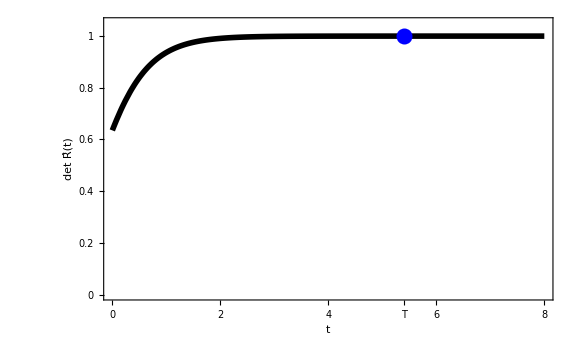

```mathematica
gg=15;
kk=0.1;
g1=Plot[order[tt],{tt,0,gg},PlotRange->{{0,gg},{0,1.05}},PlotStyle->Directive[Black,Thickness[0.007]]];
aa3=Show[g1,Graphics[{PointSize[0.02],Blue,Point[{13.38,order[13.38]}]}],AxesOrigin->{0,0},PlotRange->{{0,gg},{0,1.05}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{{0,0},{2,2},{4,4},{5.41,Style["T",Blue]},{6,6},{8,8}},None}},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,25],FrameLabel->{"t","det R̂(t)"}]
```

Step 13) Get the final figure potential function and unit sphere

```mathematica
Grid[{{cc1,aa1}}]
```

-Graphics- | -Graphics3D-